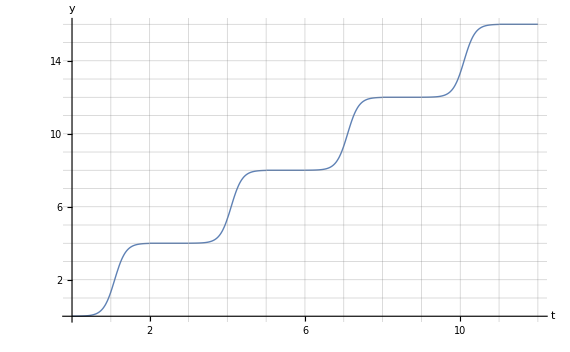

```mathematica
G[x_]:=4/(1+2Exp[-7(x-1)])
F[x_]:=Piecewise[{{G[x],0<=x<=2},{4,2≤x≤3},{G[x-3]+4,3<x≤5},{8,5<x≤6},{G[x-6]+8,6<x≤8},{12,8<x≤9},{G[x-9]+12,9<x≤11},{16,11<x≤12}}]
Plot[F[x],{x,0,12},AxesLabel->{"t","y"},GridLines->{{-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12},{-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}},Ticks->{{2,6,10},{2,6,10,14}},PlotStyle->{Thick}]
```

```mathematica
L[x_]=D[F[x],x]
```

Piecewise[{{0, x<0}, {-(28 ⅇ^(14 x))/((2 ⅇ^7+ⅇ^(7 x))^2)+(28 ⅇ^(7 x))/(2 ⅇ^7+ⅇ^(7 x)), 0<x<2}, {0, 2<x<3}, {-(56 ⅇ^(7 x) (ⅇ^28+ⅇ^(7 x)))/((2 ⅇ^28+ⅇ^(7 x))^2)+(56 ⅇ^(7 x))/(2 ⅇ^28+ⅇ^(7 x)), 3<x<5}, {0, 5<x<6}, {(84 ⅇ^(7 x))/(2 ⅇ^49+ⅇ^(7 x))-(28 ⅇ^(7 x) (4 ⅇ^49+3 ⅇ^(7 x)))/((2 ⅇ^49+ⅇ^(7 x))^2), 6<x<8}, {0, 8<x<9}, {(112 ⅇ^(7 x))/(2 ⅇ^70+ⅇ^(7 x))-(56 ⅇ^(7 x) (3 ⅇ^70+2 ⅇ^(7 x)))/((2 ⅇ^70+ⅇ^(7 x))^2), 9<x<11}, {0, 11<x<12||x>12}, {Indeterminate, True}}]

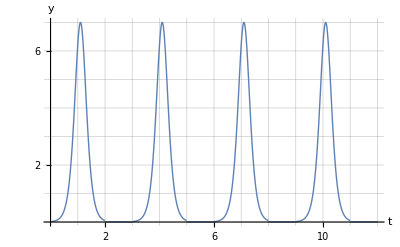

```mathematica
Plot[L[x],{x,0,12},AxesLabel->{"t","y"},GridLines->{{-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12},{-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}},Ticks->{{2,6,10},{2,6,10,14}},PlotStyle->{Thick}]
```

```mathematica
LL[x_]=D[L[x],x]
```

Piecewise[{{0, x<0}, {-(784 ⅇ^(7+14 x))/((2 ⅇ^7+ⅇ^(7 x))^3)+(392 ⅇ^(7+7 x))/((2 ⅇ^7+ⅇ^(7 x))^2), 0<x<2}, {0, 2<x<3}, {-(784 ⅇ^(28+14 x))/((2 ⅇ^28+ⅇ^(7 x))^3)+(392 ⅇ^(28+7 x))/((2 ⅇ^28+ⅇ^(7 x))^2), 3<x<5}, {0, 5<x<6}, {-(784 ⅇ^(49+14 x))/((2 ⅇ^49+ⅇ^(7 x))^3)+(392 ⅇ^(49+7 x))/((2 ⅇ^49+ⅇ^(7 x))^2), 6<x<8}, {0, 8<x<9}, {-(784 ⅇ^(70+14 x))/((2 ⅇ^70+ⅇ^(7 x))^3)+(392 ⅇ^(70+7 x))/((2 ⅇ^70+ⅇ^(7 x))^2), 9<x<11}, {0, 11<x<12||x>12}, {Indeterminate, True}}]

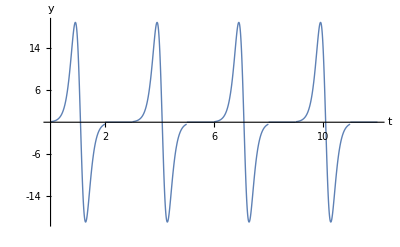

```mathematica
Plot[LL[x],{x,0,12},AxesLabel->{"t","y"},GridLines->Automatic,Ticks->{{2,6,10},{-14,-10,-6,-22,6,10,14}},PlotStyle->{Thick}]
```